```mathematica
m3a12[a_]:={{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}};
```

```mathematica
m3a13[a_]:={{Cos[a],0,-Sin[a]},{0,1,0},{Sin[a],0,Cos[a]}};
```

```mathematica
m3a23[a_]:={{1,0,0},{0,Cos[a],-Sin[a]},{0,Sin[a],Cos[s]}};
```

```mathematica
mm3[a12_,a13_]:=m3a12[a12].m3a13[a13]
```

```mathematica
mm3[x,y]//MatrixForm
```

(Cos[x] Cos[y] | -Sin[x] | -Cos[x] Sin[y]
Cos[y] Sin[x] | Cos[x] | -Sin[x] Sin[y]
Sin[y] | 0 | Cos[y])

```mathematica
rs3[m_,i_,x_,y_]:=Sum[Abs[mm3[x,y][[i]][[j]]],{j,m}]
```

```mathematica
rs3[1,1,x,y]
```

Abs[Cos[x] Cos[y]]

```mathematica
mrs3[m_,n_,x_,y_]:=Max[MapThread[rs3,{Table[m,{i,n}],Range[n],Table[x,{i,n}],Table[y,{i,n}]}]]
```

```mathematica
mrs3[2,3,x,y]
```

Max[Abs[Cos[x] Cos[y]]+Abs[Sin[x]],Abs[Cos[x]]+Abs[Cos[y] Sin[x]],Abs[Sin[y]]]

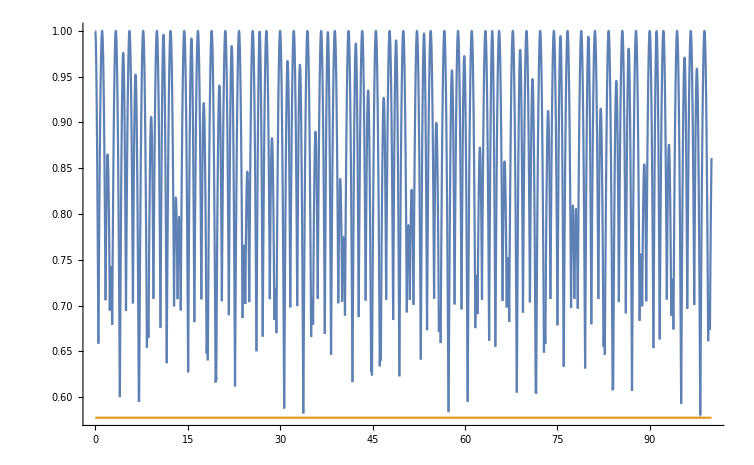

```mathematica
Plot[{mrs3[1,3,x,Sqrt[2] x],1/Sqrt[3]},{x,0,100},PlotPoints->5000]
```

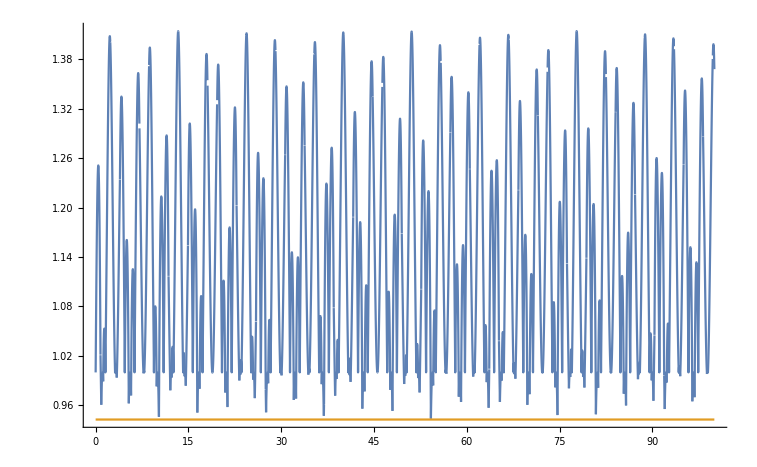

```mathematica
Plot[{mrs3[2,3,x,Sqrt[2] x],1/Sqrt[9/8]},{x,0,100},PlotPoints->5000]
```

```mathematica
mm3[a12_,a13_,a23_]:=m3a12[a12].m3a13[a13].m3a23[a23]
```

```mathematica
mm3[x,y,z]//MatrixForm
```

(Cos[x] Cos[y] | -Cos[z] Sin[x]-Cos[x] Sin[y] Sin[z] | -Cos[s] Cos[x] Sin[y]+Sin[x] Sin[z]
Cos[y] Sin[x] | Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z] | -Cos[s] Sin[x] Sin[y]-Cos[x] Sin[z]
Sin[y] | Cos[y] Sin[z] | Cos[s] Cos[y])

```mathematica
rs3[m_,i_,x_,y_,z_]:=Sum[Abs[mm3[x,y,z][[i]][[j]]],{j,m}]
```

```mathematica
mrs3[m_,n_,x_,y_,z_]:=Max[MapThread[rs3,{Table[m,{i,n}],Range[n],Table[x,{i,n}],Table[y,{i,n}],Table[z,{i,n}]}]]
```

```mathematica
mrs3[1,3,x,y,z]
```

Max[Abs[Cos[x] Cos[y]],Abs[Cos[y] Sin[x]],Abs[Sin[y]]]

```mathematica
mrs3[2,3,x,y,z]
```

Max[Abs[Sin[y]]+Abs[Cos[y] Sin[z]],Abs[Cos[x] Cos[y]]+Abs[-Cos[z] Sin[x]-Cos[x] Sin[y] Sin[z]],Abs[Cos[y] Sin[x]]+Abs[Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z]]]

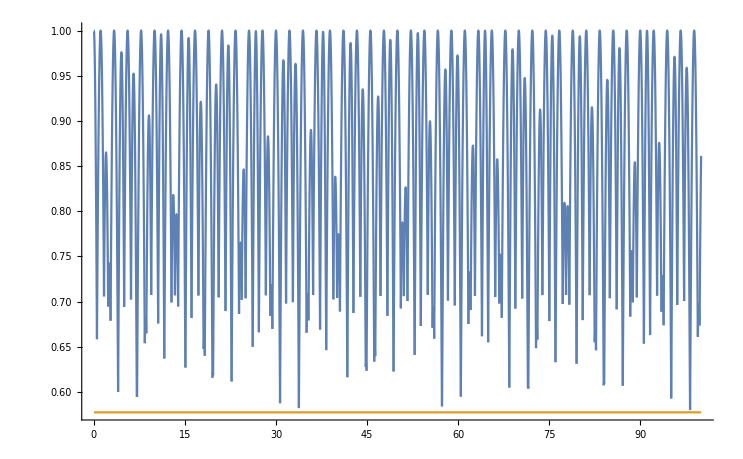

```mathematica
Plot[{mrs3[1,3,x,Sqrt[2] x,Sqrt[3]x],1/Sqrt[3]},{x,0,100},PlotPoints->5000]
```

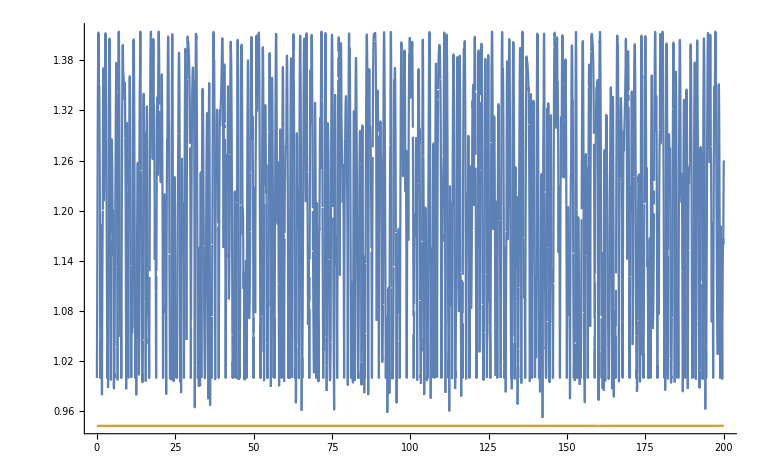

```mathematica
Plot[{mrs3[2,3,x,Sqrt[2] x,Sqrt[3]x],1/Sqrt[9/8]},{x,0,200},PlotPoints->10000]
```

```mathematica
mrs3[1,3,x,y,z]
```

Max[Abs[Cos[x] Cos[y]],Abs[Cos[y] Sin[x]],Abs[Sin[y]]]

```mathematica
mrs3[2,3,x,y,z]
```

Max[Abs[Sin[y]]+Abs[Cos[y] Sin[z]],Abs[Cos[x] Cos[y]]+Abs[-Cos[z] Sin[x]-Cos[x] Sin[y] Sin[z]],Abs[Cos[y] Sin[x]]+Abs[Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z]]]